# Define functions for MAD data

### Extract the coordinates: X,Y,Z

```mathematica
Clear[GetXYZ];
GetXYZ[x_]:=Module[
{f},
f[y_]:={y[[4]],y[[5]],y[[6]],y[[3]]};
f/@x
]
```

### Extract the coordinates: X,Y

```mathematica
Clear[GetXY];
GetXY[x_]:=Module[
{f},
f[y_]:={y[[4]],y[[5]]};
f/@x
]
```

### Generate: length, height

```mathematica
Clear[CalculateLH];
CalculateLH[x_]:=Module[
{f},
f[y_]:={√((y[[1]]-1880.1405971)^2+(y[[2]]-2090.7822669)^2),y[[3]]-2433.66};
f/@x
]
```

### Calculate distance to a line

```mathematica
Clear[CalculateDistance];
CalculateDistance[x_]:=Module[
{f,a=2.0729557841409147,b=-1.,c=-1806.666058693948},
f[y_]:={Abs[a*y[[1]]+b*y[[2]]+c]/√(a^2+b^2)};
f/@x
]
```

### tickformat

```mathematica
tickFormat[xmin_,xmax_,digits_,divisions_: 10]:=Function[tickNumber,{tickNumber,PaddedForm[Round[tickNumber,0.01],{Max@(Length@IntegerDigits@IntegerPart[#]&/@(10^digits {xmin,xmax})),digits}]}]/@FindDivisions[{xmin,xmax},divisions];
```

# Get BTP new BT old BTM old BTM new BTP.BHZ10: Path length = 1.5333988694; Ldeflect = 1.5365599935435688 BTM.BHZ10: Path length =1.5338328831; Ldeflect = 1.53721265498988324

```mathematica
fileBTBTPnew=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/PSB-PS/2014/out/BT1_BTP.survey","Table"];
fileBT=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/PSB-PS/2014/cmd/BT_28-Jun-2007.csv","CSV"];fileBTMold=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/PSB-PS/2014/cmd/BTM_23-May-2014.csv","CSV"];
fileBTMnew=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/PSB-PS/2014/cmd/matching_BTM_line/DUMMY_GPTEST.survey","Table"];
```

```mathematica
Length[fileBTBTPnew]
Length[fileBT]
Length[fileBTMold]
Length[fileBTMnew]
```

630

41

23

135

```mathematica
Clear[x];
fileBTBTPnew[[Range[9,630]]];
fileBTBTPnew[[Range[80,85]]];
fileBTBTPnew[[Range[82,135]]];
```

## BTP new

```mathematica
XYBTPlinenew=GetXY[fileBTBTPnew[[Range[82,135]]]];
BTPlinenew=LinearModelFit[XYBTPlinenew,x,x]
```

FittedModel[-609.48434425662211+1.4413131805649766 x]

## BT old

```mathematica
Clear[x];
fileBT[[Range[4,40]]]
XYBTlineold=GetXY[fileBT[[Range[4,40]]]];
BTlineold=LinearModelFit[XYBTlineold,x,x]
```

{{EJ_PT,1,E,1880.,2090.49,2433.66,0.00001,0.,28.6142,0.,0., 14-Jun-1994,},{EJ_PT,1,S,1880.,2090.49,2433.66,0.00002,0.,28.6142,0.,0., 14-Jun-1994,},{BTBVT,10,E,1881.28,2093.14,2433.66,2.94,0.,28.6142,0.,0., 23-Jan-1998,},{BTBVT,10,S,1881.62,2093.86,2433.66,3.74,0.,28.6142,0.,0., 23-Jan-1998,},{BTUES,0,E,1881.72,2094.06,2433.66,3.96763,0.,28.6142,0.,0., 14-Jun-1994,},{BTUES,0,S,1881.94,2094.52,2433.66,4.47913,0.,28.6142,0.,0., 14-Jun-1994,},{BTSMV,10,E,1882.84,2096.37,2433.66,6.53388,0.,28.6142,0.,0., 03-Feb-1999,},{BTSMV,10,S,1883.48,2097.71,2433.66,8.01888,0.,28.6142,0.,0., 03-Feb-1999,},{BTUES,10,E,1883.92,2098.62,2433.66,9.02638,0.,28.6142,0.,0., 14-Jun-1994,},{BTUES,10,S,1884.,2098.78,2433.66,9.21138,0.,28.6142,0.,0., 14-Jun-1994,},{BTQNO,10,E,1884.12,2099.02,2433.66,9.47388,0.,28.6142,0.,0., 27-Jan-1998,},{BTQNO,10,S,1884.3,2099.41,2433.66,9.90388,0.,28.6142,0.,0., 27-Jan-1998,},{BTQNO,20,E,1884.98,2100.82,2433.66,11.4739,0.,28.6142,0.,0., 27-Jan-1998,},{BTQNO,20,S,1885.17,2101.21,2433.66,11.9039,0.,28.6142,0.,0., 27-Jan-1998},{BTKFA,10,E,1886.13,2103.2,2433.66,14.1139,0.,28.6142,0.,0., 14-Jun-1994},{BTKFA,10,S,1887.1,2105.21,2433.66,16.3439,0.,28.6142,0.,0., 14-Jun-1994},{BTBVT,20,E,1887.19,2105.39,2433.66,16.5502,0.,28.6142,0.,0., 10-Feb-1999},{BTBVT,20,S,1887.54,2106.11,2433.66,17.3497,0.,28.6142,0.,0., 10-Feb-1999},{BTUES,20,E,1887.63,2106.3,2433.66,17.5549,0.,28.6142,0.,0., 14-Jun-1994},{BTUES,20,S,1887.71,2106.47,2433.66,17.7399,0.,28.6142,0.,0., 14-Jun-1994},{BTSMV,20,E,1888.92,2108.98,2433.66,20.5289,0.,28.6142,0.,0., 14-Jun-1994},{BTSMV,20,S,1889.57,2110.32,2433.66,22.0189,0.,28.6142,0.,0., 14-Jun-1994},{BTQNO,30,E,1889.73,2110.66,2433.66,22.3939,0.,28.6142,0.,0., 27-Jan-1998},{BTQNO,30,S,1889.92,2111.05,2433.66,22.8239,0.,28.6142,0.,0., 27-Jan-1998},{BTSMV,30,E,1889.97,2111.15,2433.66,22.9419,0.,28.6142,0.,0., 14-Jun-1994},{BTSMV,30,S,1890.34,2111.93,2433.66,23.8059,0.,28.6142,0.,0., 14-Jun-1994},{BTUES,30,E,1891.26,2113.84,2433.66,25.9244,0.,28.6142,0.,0., 14-Jun-1994},{BTUES,30,S,1891.4,2114.12,2433.66,26.2424,0.,28.6142,0.,0., 14-Jun-1994},{BTKFA,20,E,1892.63,2116.66,2433.66,29.0629,0.,28.6142,0.,0., 14-Jun-1994},{BTKFA,20,S,1893.6,2118.67,2433.66,31.2929,0.,28.6142,0.,0., 14-Jun-1994},{BTQNO,40,E,1893.82,2119.15,2433.66,31.8189,0.,28.6142,0.,0., 27-Jan-1998},{BTQNO,40,S,1894.01,2119.53,2433.66,32.2489,0.,28.6142,0.,0., 27-Jan-1998},{BTUES,40,E,1894.1,2119.71,2433.66,32.4489,0.,28.6142,0.,0., 14-Jun-1994},{BTUES,40,S,1894.18,2119.88,2433.66,32.6339,0.,28.6142,0.,0., 14-Jun-1994},{BTQNO,50,E,1894.4,2120.35,2433.66,33.1539,0.,28.6142,0.,0., 14-Jun-1994},{BTQNO,50,S,1894.62,2120.8,2433.66,33.6539,0.,28.6142,0.,0., 14-Jun-1994},{BTBHZ,10,E,1895.01,2121.61,2433.66,34.555,0.,28.6142,0.081195,0., 14-Jun-1994}}

FittedModel[-1806.67+2.07296 x]

## BT new

```mathematica
Clear[x];
fileBTMnew[[Range[9,82]]]
XYBTlinenew=GetXY[fileBTMnew[[Range[9,82]]]];
BTlinenew=LinearModelFit[XYBTlinenew,x,x]
```

{{BT1BTM$START,0.,0.,1880.14059710663469,2090.7822669027646,2432.94000000000006},{BTDUMMY$START,0.,0.,1880.14059710663469,2090.7822669027646,2432.94000000000006},{BT1.START,0.,0.,1880.14059710663469,2090.7822669027646,2432.94000000000006},{DRIFT_0,2.54897,2.54897,1881.24809526711988,2093.07806162046745,2432.94000000000006},{BT1.BVT10,3.45579,0.906823,1881.64171283818519,2093.89401344114685,2432.97480508696162},{DRIFT_1,3.6107,0.154908,1881.70882034380156,2094.03312433307337,2432.98669040595951},{BT1.BPM00,4.1187,0.508,1881.9288902666583,2094.48931955257467,2433.02566669051885},{DRIFT_2,4.29897,0.180274,1882.00698643252963,2094.65120945133685,2433.03949819618083},{BT1.DHZ10,4.63397,0.335,1882.15211128323244,2094.95204685002364,2433.06520106099833},{DRIFT_3,4.67824,0.0442716,1882.17129013008048,2094.99180375153037,2433.06859780046443},{BT1.VVS10,4.77824,0.1,1882.21461098103646,2095.08160596009338,2433.0762702974248},{DRIFT_4,6.37449,1.59625,1882.90612107006018,2096.51507579892723,2433.19874270826404},{BT1.SMV10,7.3713,0.996808,1883.33877916625511,2097.41195690198993,2433.23861525886832},{DRIFT_5,7.47312,0.101815,1883.38301662776098,2097.5036592036945,2433.23894507970363},{BT2.BTV10,7.47312,0.,1883.38301662776098,2097.5036592036945,2433.23894507970363},{DRIFT_6,8.15312,0.680004,1883.67846931820532,2098.11611956729121,2433.24114788361294},{BT.VPG11,8.15312,0.,1883.67846931820532,2098.11611956729121,2433.24114788361294},{DRIFT_7,8.71062,0.557503,1883.92069728891829,2098.61824744026126,2433.24295386046833},{BT2.BPM10,8.89562,0.185,1884.00107737947565,2098.78487181391211,2433.24355314957074},{DRIFT_8,9.14013,0.244502,1884.10731022319919,2099.00508780177461,2433.24434518880753},{BT1.QNO10,9.60614,0.466017,1884.30978221635337,2099.42480329111004,2433.24815220803157},{DRIFT_9,10.7542,1.1481,1884.80857773663206,2100.4587843499753,2433.26319119930213},{BT2.VVS30,10.8542,0.1,1884.85202293447924,2100.54884432414565,2433.26450109869893},{DRIFT_10,11.1403,0.286029,1884.97628873762164,2100.80644183954064,2433.26824778898117},{BT1.QNO20,11.6063,0.466028,1885.17876073077582,2101.22615732887653,2433.27329624251615},{DRIFT_11,13.5189,1.91257,1886.00972142083015,2102.94870209771852,2433.28968096627932},{BT.VGP21,13.5189,0.,1886.00972142083015,2102.94870209771852,2433.28968096627932},{BT.VGR21,13.5189,0.,1886.00972142083015,2102.94870209771852,2433.28968096627932},{BT.VPI22,13.5189,0.,1886.00972142083015,2102.94870209771852,2433.28968096627932},{BT.VPI22A,13.5189,0.,1886.00972142083015,2102.94870209771852,2433.28968096627932},{DRIFT_12,13.9434,0.424516,1886.19416211452949,2103.33103950055374,2433.29331773255854},{BT1.KFA10,15.5034,1.56002,1886.87196535341468,2104.73609564511071,2433.3000000071811},{DRIFT_13,15.9109,0.4075,1887.04901972026164,2105.10312151897369,2433.30000000718064},{BT.BTV20,15.9109,0.,1887.04901972026164,2105.10312151897369,2433.30000000718064},{DRIFT_14,16.1673,0.256386,1887.16041653733942,2105.33404219526983,2433.30000000718019},{BT2.BVT20,17.0811,0.913809,1887.55709296097734,2106.15633488208277,2433.33387495579791},{DRIFT_15,17.3725,0.291398,1887.68335419484765,2106.41806883714708,2433.35546932839225},{BT2.BPM20,17.5575,0.185,1887.76351369005238,2106.58423592638565,2433.36917895210945},{DRIFT_16,18.7631,1.20563,1888.28590659921883,2107.66713332903646,2433.45852345457752},{BT2.DVT40,19.0981,0.335,1888.43106027972476,2107.96803049063055,2433.48334898941675},{DRIFT_17,20.0844,0.986272,1888.85840677554324,2108.85390088096983,2433.55643776872512},{BT.VPI23,20.0844,0.,1888.85840677554324,2108.85390088096983,2433.55643776872512},{DRIFT_18,20.3895,0.305109,1888.99060897543518,2109.12795019591204,2433.57904822068031},{BT2.SMV20,21.3864,0.996845,1889.42331435162009,2110.02492930830294,2433.61742800756565},{DRIFT_19,21.4733,0.0869357,1889.46108682599743,2110.10322997754474,2433.61767697634741},{BT2.BTV30,21.4733,0.,1889.46108682599743,2110.10322997754474,2433.61767697634741},{DRIFT_20,22.0713,0.598002,1889.72091138776818,2110.6418348057291,2433.61938955159303},{BT2.QNO30,22.5373,0.466004,1889.92338338092236,2111.06155029506499,2433.62131790199237},{DRIFT_21,25.6038,3.06655,1891.25574572103051,2113.8234785145637,2433.63791490784479},{BT.BPM30,25.9258,0.322,1891.39564921224041,2114.11349226588891,2433.63965766129286},{DRIFT_22,26.1699,0.244008,1891.50166661367189,2114.33326165140625,2433.64097830161654},{BT.BCT10,26.4839,0.314,1891.6380942417461,2114.61607009213958,2433.6426777568422},{DRIFT_23,26.6979,0.214009,1891.73107732586732,2114.80881991419574,2433.64383603094302},{BT.DVT50,27.1339,0.436,1891.92051186676031,2115.20150934145568,2433.64619578405927},{DRIFT_24,27.9081,0.774215,1892.25689483909423,2115.89881636964174,2433.65038604821802},{BT.VGP23,27.9081,0.,1892.25689483909423,2115.89881636964174,2433.65038604821802},{BT.VPG22,27.9081,0.,1892.25689483909423,2115.89881636964174,2433.65038604821802},{DRIFT_25,28.9044,0.996315,1892.68977648862278,2116.79616088887997,2433.65577837960882},{BT2.KFA20,30.4644,1.56001,1893.3675797275082,2118.20121703343693,2433.65999998719872},{DRIFT_26,30.8719,0.4075,1893.54463409568143,2118.56824291004887,2433.65999998719781},{BT.BTV40,30.8719,0.,1893.54463409568143,2118.56824291004887,2433.65999998719781},{DRIFT_27,31.0214,0.1495,1893.60959023940791,2118.7028941239023,2433.65999998719735},{BT.DVT60,31.4574,0.436,1893.79902755489115,2119.0955893027658,2433.65999998719644},{DRIFT_28,31.4964,0.03895,1893.81595091140048,2119.13067067252905,2433.65999998719644},{BT.QNO40,31.9625,0.4661,1894.01846635348034,2119.55047622956636,2433.65999998719553},{DRIFT_29,32.2144,0.25195,1894.12793592145295,2119.77740180368255,2433.65999998719508},{BT.BPM40,32.3994,0.185,1894.20831643375664,2119.94402705159473,2433.65999998719462},{DRIFT_30,32.9054,0.506,1894.42816799713864,2120.3997696215597,2433.65999998719371},{BT.QNO50,33.2934,0.388,1894.59674982834849,2120.74923230366721,2433.65999998719281},{DRIFT_31,33.3,0.00659882,1894.59961694473873,2120.75517570917236,2433.65999998719281},{END.DUMMY,33.3,0.,1894.59961694473873,2120.75517570917236,2433.65999998719281},{BTDUMMY$END,33.3,0.,1894.59961694473873,2120.75517570917236,2433.65999998719281},{DRIFT_62,34.2508,0.95081,1895.01273381339001,2121.61154871156941,2433.65999998719099},{BTM$START,34.2508,0.,1895.01273381339001,2121.61154871156941,2433.65999998719099}}

FittedModel[-1806.66605886791378+2.07295578414108827 x]

## BTM old

```mathematica
Clear[x];
fileBTMold[[Range[4,23]]]
XYBTMlineold=GetXY[fileBTMold[[Range[4,23]]]]
```

{{360,BTM,DEPFA.1.E,1895.56,2123.04,2433.66,0.00001,,0,0,0,18.2759,0,14-Dec-95,156377},{360,BTM,DEPFA.1.S,1895.64,2123.29,2433.66,0.25513,0.25512,0,0,0,18.2759,0,14-Dec-95,156378},{360,BTM,BTMMTV.10.E,1895.93,2124.29,2433.66,1.30313,,0,0,0,18.2759,0,14-Dec-95,139040},{360,BTM,BTMMTV.10.S,1895.99,2124.48,2433.66,1.50313,0.2,0,0,0,18.2759,0,14-Dec-95,139041},{360,BTM,BTMQNO.5.E,1896.06,2124.71,2433.66,1.73763,,0,0,0,18.2759,0,14-Dec-95,139038},{360,BTM,BTMQNO.5.S,1896.2,2125.19,2433.66,2.23763,0.5,0,0,0,18.2759,0,14-Dec-95,139039},{360,BTM,BTMBHZ.10.E,1896.35,2125.69,2433.66,2.76108,,0.17537,0,0,18.2759,0,14-Dec-95,139042},{360,BTM,BTMBHZ.10.S,1896.59,2127.88,2433.66,4.96108,2.2,0.17537,0,0,395.947,0,14-Dec-95,139043},{360,BTM,BTMQNO.10.E,1896.56,2128.32,2433.66,5.40903,,0,0,0,395.947,0,14-Dec-95,139044},{360,BTM,BTMQNO.10.S,1896.53,2128.82,2433.66,5.90903,0.5,0,0,0,395.947,0,14-Dec-95,139045},{360,BTM,BTMDVT.10.E,1896.51,2129.16,2433.66,6.25303,,0,0,0,395.947,0,14-Dec-95,139046},{360,BTM,BTMDVT.10.S,1896.49,2129.45,2433.66,6.53503,0.282,0,0,0,395.947,0,14-Dec-95,139047},{360,BTM,BTMDHZ.10.E,1896.48,2129.63,2433.66,6.71703,,0,0,0,395.947,0,14-Dec-95,139050},{360,BTM,BTMDHZ.10.S,1896.46,2129.91,2433.66,6.99903,0.282,0,0,0,395.947,0,14-Dec-95,139051},{360,BTM,BTMQNO.20.E,1896.44,2130.2,2433.66,7.29203,,0,0,0,395.947,0,14-Dec-95,139048},{360,BTM,BTMQNO.20.S,1896.41,2130.7,2433.66,7.79203,0.5,0,0,0,395.947,0,14-Dec-95,139049},{360,BTM,BTMUES.0.E,1896.4,2130.91,2433.66,7.99753,,0,0,0,395.947,0,14-Dec-95,139054},{360,BTM,BTMUES.0.S,1896.39,2131.09,2433.66,8.18253,0.185,0,0,0,395.947,0,14-Dec-95,139055},{360,BTM,BTMMTV.15.E,1896.37,2131.27,2433.66,8.36653,,0,0,0,395.947,0,14-Dec-95,139052},{360,BTM,BTMMTV.15.S,1896.36,2131.47,2433.66,8.56653,0.2,0,0,0,395.947,0,14-Dec-95,139053}}

{{1895.56,2123.04},{1895.64,2123.29},{1895.93,2124.29},{1895.99,2124.48},{1896.06,2124.71},{1896.2,2125.19},{1896.35,2125.69},{1896.59,2127.88},{1896.56,2128.32},{1896.53,2128.82},{1896.51,2129.16},{1896.49,2129.45},{1896.48,2129.63},{1896.46,2129.91},{1896.44,2130.2},{1896.41,2130.7},{1896.4,2130.91},{1896.39,2131.09},{1896.37,2131.27},{1896.36,2131.47}}

## BTM1 old

```mathematica
Clear[x];
fileBTMold[[Range[4,10]]]
XYBTM1lineold=GetXY[fileBTMold[[Range[4,10]]]];
BTM1lineold=LinearModelFit[XYBTM1lineold,x,x]
```

{{360,BTM,DEPFA.1.E,1895.56,2123.04,2433.66,0.00001,,0,0,0,18.2759,0,14-Dec-95,156377},{360,BTM,DEPFA.1.S,1895.64,2123.29,2433.66,0.25513,0.25512,0,0,0,18.2759,0,14-Dec-95,156378},{360,BTM,BTMMTV.10.E,1895.93,2124.29,2433.66,1.30313,,0,0,0,18.2759,0,14-Dec-95,139040},{360,BTM,BTMMTV.10.S,1895.99,2124.48,2433.66,1.50313,0.2,0,0,0,18.2759,0,14-Dec-95,139041},{360,BTM,BTMQNO.5.E,1896.06,2124.71,2433.66,1.73763,,0,0,0,18.2759,0,14-Dec-95,139038},{360,BTM,BTMQNO.5.S,1896.2,2125.19,2433.66,2.23763,0.5,0,0,0,18.2759,0,14-Dec-95,139039},{360,BTM,BTMBHZ.10.E,1896.35,2125.69,2433.66,2.76108,,0.17537,0,0,18.2759,0,14-Dec-95,139042}}

FittedModel[-4297.57+3.38718 x]

## BTM2 old

```mathematica
Clear[x];
fileBTMold[[Range[11,23]]]
XYBTM2lineold=GetXY[fileBTMold[[Range[11,23]]]];
BTM2lineold=LinearModelFit[XYBTM2lineold,x,x]
```

{{360,BTM,BTMBHZ.10.S,1896.59,2127.88,2433.66,4.96108,2.2,0.17537,0,0,395.947,0,14-Dec-95,139043},{360,BTM,BTMQNO.10.E,1896.56,2128.32,2433.66,5.40903,,0,0,0,395.947,0,14-Dec-95,139044},{360,BTM,BTMQNO.10.S,1896.53,2128.82,2433.66,5.90903,0.5,0,0,0,395.947,0,14-Dec-95,139045},{360,BTM,BTMDVT.10.E,1896.51,2129.16,2433.66,6.25303,,0,0,0,395.947,0,14-Dec-95,139046},{360,BTM,BTMDVT.10.S,1896.49,2129.45,2433.66,6.53503,0.282,0,0,0,395.947,0,14-Dec-95,139047},{360,BTM,BTMDHZ.10.E,1896.48,2129.63,2433.66,6.71703,,0,0,0,395.947,0,14-Dec-95,139050},{360,BTM,BTMDHZ.10.S,1896.46,2129.91,2433.66,6.99903,0.282,0,0,0,395.947,0,14-Dec-95,139051},{360,BTM,BTMQNO.20.E,1896.44,2130.2,2433.66,7.29203,,0,0,0,395.947,0,14-Dec-95,139048},{360,BTM,BTMQNO.20.S,1896.41,2130.7,2433.66,7.79203,0.5,0,0,0,395.947,0,14-Dec-95,139049},{360,BTM,BTMUES.0.E,1896.4,2130.91,2433.66,7.99753,,0,0,0,395.947,0,14-Dec-95,139054},{360,BTM,BTMUES.0.S,1896.39,2131.09,2433.66,8.18253,0.185,0,0,0,395.947,0,14-Dec-95,139055},{360,BTM,BTMMTV.15.E,1896.37,2131.27,2433.66,8.36653,,0,0,0,395.947,0,14-Dec-95,139052},{360,BTM,BTMMTV.15.S,1896.36,2131.47,2433.66,8.56653,0.2,0,0,0,395.947,0,14-Dec-95,139053}}

FittedModel[31880.-15.6871 x]

## BTM new

```mathematica
Clear[x];
fileBTMnew[[Range[84,133]]]
XYBTMlinenew=GetXY[fileBTMnew[[Range[84,133]]]];
```

{{BT.BHZ10,35.7846,1.53383,1895.56431508869127,2123.04096662882967,2433.6599999871878},{DRIFT_33,36.8581,1.07349,1895.8682736959729,2124.07052858906718,2433.65999998718553},{BTM.VVS10,36.8581,0.,1895.8682736959729,2124.07052858906718,2433.65999998718553},{DRIFT_34,37.191,0.3329,1895.96253398176282,2124.38980497172452,2433.65999998718507},{BTM.BTV10,37.191,0.,1895.96253398176282,2124.38980497172452,2433.65999998718507},{DRIFT_35,37.4955,0.3045,1896.04875283734418,2124.68184359749557,2433.65999998718462},{BTM.QNO05,38.0555,0.56,1896.20731624990754,2125.21892612764941,2433.65999998718371},{DRIFT_36,38.4918,0.436283,1896.33084939663127,2125.63735490593808,2433.6599999871828},{BTM_1$END,38.4918,0.,1896.33084939663127,2125.63735490593808,2433.6599999871828},{BTM_2$START,38.4918,0.,1896.33084939663127,2125.63735490593808,2433.6599999871828},{BTM.BHZ10,40.8429,2.35103,1896.59159075840057,2127.96177632690797,2433.65999998717825},{DRIFT_37,41.1901,0.347283,1896.56949751895468,2128.30835611535849,2433.6599999871778},{BTM.QNO10,41.7501,0.56,1896.53387180472896,2128.8672217597541,2433.65999998717689},{DRIFT_38,42.0556,0.3055,1896.51443670527192,2129.17210292825939,2433.65999998717643},{BTM.DVT10,42.3556,0.3,1896.49535150122233,2129.47149523775715,2433.65999998717598},{DRIFT_39,42.5196,0.164,1896.48491825634187,2129.63516303361575,2433.65999998717552},{BTM.DHZ10,42.8196,0.3,1896.46583305229228,2129.93455534311352,2433.65999998717507},{DRIFT_40,43.0736,0.254,1896.44967424619699,2130.18804083182158,2433.65999998717462},{BTM.QNO20,43.6336,0.56,1896.41404853197128,2130.74690647621719,2433.65999998717371},{DRIFT_41,43.9016,0.268,1896.39699908302032,2131.0143636060352,2433.65999998717325},{BTM.BPM00,43.9016,0.,1896.39699908302032,2131.0143636060352,2433.65999998717325},{DRIFT_42,44.2831,0.3815,1896.37272906520389,2131.39509082628001,2433.6599999871728},{BTM.BTV15,44.2831,0.,1896.37272906520389,2131.39509082628001,2433.6599999871728},{DRIFT_43,44.4831,0.2,1896.36000559583749,2131.59468569927867,2433.65999998717234},{BTM.VPI11,44.4831,0.,1896.36000559583749,2131.59468569927867,2433.65999998717234},{DRIFT_44,45.082,0.59883,1896.32190964074653,2132.19230236334988,2433.65999998717143},{BTY.BVT101,46.2263,1.14434,1896.24910972464841,2133.33432499802029,2433.65999998716961},{DRIFT_45,47.0751,0.84883,1896.19510943284945,2134.18143525333926,2433.65999998716825},{BTM.VPI11A,47.0751,0.,1896.19510943284945,2134.18143525333926,2433.65999998716825},{DRIFT_46,47.7591,0.684,1896.15159516761651,2134.86404971899401,2433.65999998716688},{BTM.BSGH01,47.7591,0.,1896.15159516761651,2134.86404971899401,2433.65999998716688},{BTM.BSGV01,47.7591,0.,1896.15159516761651,2134.86404971899401,2433.65999998716688},{DRIFT_47,50.2591,2.5,1895.99255180053706,2137.35898563147521,2433.65999998716234},{BTM.BSGH02,50.2591,0.,1895.99255180053706,2137.35898563147521,2433.65999998716234},{BTM.BSGV02,50.2591,0.,1895.99255180053706,2137.35898563147521,2433.65999998716234},{DRIFT_48,51.0466,0.7875,1895.942453139907,2138.14489044390666,2433.65999998716097},{BTM.BPM10,51.0466,0.,1895.942453139907,2138.14489044390666,2433.65999998716097},{DRIFT_49,52.0931,1.0465,1895.87587758644759,2139.18927061687145,2433.65999998715915},{BTM.BTV20,52.0931,0.,1895.87587758644759,2139.18927061687145,2433.65999998715915},{DRIFT_50,52.7591,0.666,1895.83350843345761,2139.8539215439564,2433.65999998715779},{BTM.BSGH03,52.7591,0.,1895.83350843345761,2139.8539215439564,2433.65999998715779},{BTM.BSGV03,52.7591,0.,1895.83350843345761,2139.8539215439564,2433.65999998715779},{DRIFT_51,53.0311,0.272,1895.81620451511935,2140.12537057123427,2433.65999998715734},{BTM.BCT10,53.0311,0.,1895.81620451511935,2140.12537057123427,2433.65999998715734},{DRIFT_52,59.8186,6.7875,1895.38440177349867,2146.89912157362051,2433.65999998714551},{BTM.TDU10,59.8186,0.,1895.38440177349867,2146.89912157362051,2433.65999998714551},{DRIFT_53,64.4918,4.67318,1895.08710616384133,2151.56284007240265,2433.65999998713733},{BTM_2$END,64.4918,0.,1895.08710616384133,2151.56284007240265,2433.65999998713733},{DRIFT_54,74.2508,9.75899,1894.46626510039914,2161.30206210705183,2433.6599999871205},{BTM$END,74.2508,0.,1894.46626510039914,2161.30206210705183,2433.6599999871205}}

## BTM1 new

```mathematica
Clear[x];
fileBTMnew[[Range[84,93]]]
XYBTM1linenew=GetXY[fileBTMnew[[Range[84,93]]]];
BTM1linenew=LinearModelFit[XYBTM1linenew,x,x]
```

{{BT.BHZ10,35.7846,1.53383,1895.56431508869127,2123.04096662882967,2433.6599999871878},{DRIFT_33,36.8581,1.07349,1895.8682736959729,2124.07052858906718,2433.65999998718553},{BTM.VVS10,36.8581,0.,1895.8682736959729,2124.07052858906718,2433.65999998718553},{DRIFT_34,37.191,0.3329,1895.96253398176282,2124.38980497172452,2433.65999998718507},{BTM.BTV10,37.191,0.,1895.96253398176282,2124.38980497172452,2433.65999998718507},{DRIFT_35,37.4955,0.3045,1896.04875283734418,2124.68184359749557,2433.65999998718462},{BTM.QNO05,38.0555,0.56,1896.20731624990754,2125.21892612764941,2433.65999998718371},{DRIFT_36,38.4918,0.436283,1896.33084939663127,2125.63735490593808,2433.6599999871828},{BTM_1$END,38.4918,0.,1896.33084939663127,2125.63735490593808,2433.6599999871828},{BTM_2$START,38.4918,0.,1896.33084939663127,2125.63735490593808,2433.6599999871828}}

FittedModel[-4297.57310794310618+3.38717817352006989 x]

## BTM2 new

```mathematica
Clear[x];
fileBTMnew[[Range[94,133]]]
XYBTM2linenew=GetXY[fileBTMnew[[Range[94,133]]]];
BTM2linenew=LinearModelFit[XYBTM2linenew,x,x]
```

{{BTM.BHZ10,40.8429,2.35103,1896.59159075840057,2127.96177632690797,2433.65999998717825},{DRIFT_37,41.1901,0.347283,1896.56949751895468,2128.30835611535849,2433.6599999871778},{BTM.QNO10,41.7501,0.56,1896.53387180472896,2128.8672217597541,2433.65999998717689},{DRIFT_38,42.0556,0.3055,1896.51443670527192,2129.17210292825939,2433.65999998717643},{BTM.DVT10,42.3556,0.3,1896.49535150122233,2129.47149523775715,2433.65999998717598},{DRIFT_39,42.5196,0.164,1896.48491825634187,2129.63516303361575,2433.65999998717552},{BTM.DHZ10,42.8196,0.3,1896.46583305229228,2129.93455534311352,2433.65999998717507},{DRIFT_40,43.0736,0.254,1896.44967424619699,2130.18804083182158,2433.65999998717462},{BTM.QNO20,43.6336,0.56,1896.41404853197128,2130.74690647621719,2433.65999998717371},{DRIFT_41,43.9016,0.268,1896.39699908302032,2131.0143636060352,2433.65999998717325},{BTM.BPM00,43.9016,0.,1896.39699908302032,2131.0143636060352,2433.65999998717325},{DRIFT_42,44.2831,0.3815,1896.37272906520389,2131.39509082628001,2433.6599999871728},{BTM.BTV15,44.2831,0.,1896.37272906520389,2131.39509082628001,2433.6599999871728},{DRIFT_43,44.4831,0.2,1896.36000559583749,2131.59468569927867,2433.65999998717234},{BTM.VPI11,44.4831,0.,1896.36000559583749,2131.59468569927867,2433.65999998717234},{DRIFT_44,45.082,0.59883,1896.32190964074653,2132.19230236334988,2433.65999998717143},{BTY.BVT101,46.2263,1.14434,1896.24910972464841,2133.33432499802029,2433.65999998716961},{DRIFT_45,47.0751,0.84883,1896.19510943284945,2134.18143525333926,2433.65999998716825},{BTM.VPI11A,47.0751,0.,1896.19510943284945,2134.18143525333926,2433.65999998716825},{DRIFT_46,47.7591,0.684,1896.15159516761651,2134.86404971899401,2433.65999998716688},{BTM.BSGH01,47.7591,0.,1896.15159516761651,2134.86404971899401,2433.65999998716688},{BTM.BSGV01,47.7591,0.,1896.15159516761651,2134.86404971899401,2433.65999998716688},{DRIFT_47,50.2591,2.5,1895.99255180053706,2137.35898563147521,2433.65999998716234},{BTM.BSGH02,50.2591,0.,1895.99255180053706,2137.35898563147521,2433.65999998716234},{BTM.BSGV02,50.2591,0.,1895.99255180053706,2137.35898563147521,2433.65999998716234},{DRIFT_48,51.0466,0.7875,1895.942453139907,2138.14489044390666,2433.65999998716097},{BTM.BPM10,51.0466,0.,1895.942453139907,2138.14489044390666,2433.65999998716097},{DRIFT_49,52.0931,1.0465,1895.87587758644759,2139.18927061687145,2433.65999998715915},{BTM.BTV20,52.0931,0.,1895.87587758644759,2139.18927061687145,2433.65999998715915},{DRIFT_50,52.7591,0.666,1895.83350843345761,2139.8539215439564,2433.65999998715779},{BTM.BSGH03,52.7591,0.,1895.83350843345761,2139.8539215439564,2433.65999998715779},{BTM.BSGV03,52.7591,0.,1895.83350843345761,2139.8539215439564,2433.65999998715779},{DRIFT_51,53.0311,0.272,1895.81620451511935,2140.12537057123427,2433.65999998715734},{BTM.BCT10,53.0311,0.,1895.81620451511935,2140.12537057123427,2433.65999998715734},{DRIFT_52,59.8186,6.7875,1895.38440177349867,2146.89912157362051,2433.65999998714551},{BTM.TDU10,59.8186,0.,1895.38440177349867,2146.89912157362051,2433.65999998714551},{DRIFT_53,64.4918,4.67318,1895.08710616384133,2151.56284007240265,2433.65999998713733},{BTM_2$END,64.4918,0.,1895.08710616384133,2151.56284007240265,2433.65999998713733},{DRIFT_54,74.2508,9.75899,1894.46626510039914,2161.30206210705183,2433.6599999871205},{BTM$END,74.2508,0.,1894.46626510039914,2161.30206210705183,2433.6599999871205}}

FittedModel[31880.063721757543-15.6871421820095157 x]

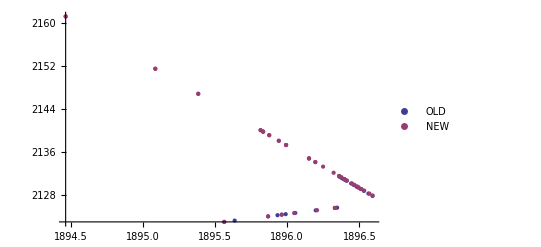

```mathematica
ListPlot[{XYBTMlineold,XYBTMlinenew},PlotLegends->{"OLD","NEW"}]
```

# Plot BTM (rotated)

```mathematica
Clear[x,F,fineF];
F=0;fineF=0;
```

```mathematica
XRoughMinOLD
```

1919.17

```mathematica
Module[{XRoughMinOLD,XRoughMaxOLD,
XFineMinOLD,XFineMaxOLD,
XExtraFineMinOLD,XExtraFineMaxOLD},
Manipulate[
If[XRoughMin>XRoughMax,XRoughMin=XRoughMax];
If[XFineMin>XFineMax,XFineMin=XFineMax];
If[XExtraFineMin>XExtraFineMax,XExtraFineMin=XExtraFineMax];
If[XMin>XMax,XMin=XMax];

If [XRoughMinOLD!=XRoughMin,XFineMin=XRoughMin;XExtraFineMin=XRoughMin;XMin=XRoughMin];
If [XFineMinOLD!=XFineMin,XExtraFineMin=XFineMin;XMin=XFineMin];
If [XExtraFineMinOLD!=XExtraFineMin,XMin=XFineMin];
If [XRoughMaxOLD!=XRoughMax,XFineMax=XRoughMax;XExtraFineMax=XRoughMax;XMax=XRoughMax];
If [XFineMaxOLD!=XFineMax,XExtraFineMax=XFineMax;XMax=XFineMax];
If [XExtraFineMaxOLD!=XExtraFineMax,XMax=XFineMax];

If[XFineMin<XRoughMin,XFineMin=XRoughMin];
If[XFineMax<XRoughMin,XFineMax=XRoughMin];
If[XFineMax>XRoughMax,XFineMax=XRoughMax];
If[XFineMin>XRoughMax,XFineMin=XRoughMax];
If[XExtraFineMin<XFineMin,XExtraFineMin=XFineMin];
If[XExtraFineMax<XFineMin,XExtraFineMax=XFineMin];
If[XExtraFineMax>XFineMax,XExtraFineMax=XFineMax];
If[XExtraFineMin>XFineMax,XExtraFineMin=XFineMax];
If[XMin<XExtraFineMin,XMin=XExtraFineMin];
If[XMax<XExtraFineMin,XMax=XExtraFineMin];
If[XMax>XExtraFineMax,XMax=XExtraFineMax];
If[XMin>XExtraFineMax,XMin=XExtraFineMax];


xa=XMin;
xb=XMax;
xd=(xb-xa)/10;
ya=YMin;
yb=YMax;
yd=(yb-ya)/10;
r=RotationTransform[Pi*(F+fineF),{1926.9590333711706,2155.5643150886913}];
BTMnew=r[XYBTMlinenew];
PlotBTMnew=ListPlot[BTMnew,PlotStyle->{Directive[Red,PointSize[Large]]}];
BTMold=r[XYBTMlineold];
PlotBTMold=ListPlot[BTMold,PlotStyle->{Directive[Blue,PointSize[Medium]]}];
xminBTM=Min[Join[BTMnew[[All,1]], BTMold[[All,1]]]];
xmaxBTM=Max[Join[BTMnew[[All,1]], BTMold[[All,1]]]];
yminBTM=Min[Join[BTMnew[[All,2]], BTMold[[All,2]]]];
ymaxBTM=Max[Join[BTMnew[[All,2]], BTMold[[All,2]]]];


XRoughMinOLD=XRoughMin;XRoughMaxOLD=XRoughMax;
XFineMinOLD=XFineMin;XFineMaxOLD=XFineMax;
XExtraFineMinOLD=XExtraFineMin;XExtraFineMaxOLD=XExtraFineMax;


Show[
Plot[{0,0},{x,0,100},PlotRange->{{xa,xb},{ya,yb}},ImageSize->800,PlotStyle->{Directive[Red,PointSize[Large]],Directive[Blue,PointSize[Medium]]},PlotLegends->Placed[{"new","old"},Above],
Ticks->{
{xa,xa+xd,xa+2*xd,xa+3*xd,xa+4*xd,xa+5*xd,xa+6*xd,xa+7*xd,xa+8*xd,xa+9*xd,xb},{ya,ya+yd,ya+2*yd,ya+3*yd,ya+4*yd,ya+5*yd,ya+6*yd,ya+7*yd,ya+8*yd,ya+9*yd,yb}
}],
ListPlot[BTMnew,PlotStyle->{Directive[Red,PointSize[Large]]}],
ListPlot[r[XYBTMlineold],PlotStyle->{Directive[Blue,PointSize[Medium]]}]],


{{XRoughMin,xminBTM},xminBTM,xmaxBTM},{{XRoughMax,xmaxBTM},xminBTM,xmaxBTM},
{{XFineMin,XRoughMin},XRoughMin,XRoughMax},{{XFineMax,XRoughMax},XRoughMin,XRoughMax},
{{XExtraFineMin,XFineMin},XFineMin,XFineMax},{{XExtraFineMax,XFineMax},XFineMin,XFineMax},
{{XMin,XExtraFineMin},XExtraFineMin,XExtraFineMax},{{XMax,XExtraFineMax},XExtraFineMin,XExtraFineMax},
{{YRoughMin,yminBTM},yminBTM,ymaxBTM},{{YRoughMax,ymaxBTM},yminBTM,ymaxBTM},
{{YMin,YRoughMin},YRoughMin,YRoughMax},{{YMax,YRoughMax},YRoughMin,YRoughMax}
]]
```

```mathematica
Control[{F,0,1}]
Control[{fineF,0,0.1}]
```

```mathematica
xa
```

1919.17

```mathematica
xb
```

1957.43

# Deflection angle BT-BTM1 from Tobias’ survey (old)

```mathematica
a1=BTlineold[[1,2,1]]
a2=BTlineold[[1,2,2]]
b1=BTM1lineold[[1,2,1]]
b2=BTM1lineold[[1,2,2]]

Clear[BTBTM1angleold];
BTBTM1angleold=BTBTM1angleold/.Solve[Tan[BTBTM1angleold]==Abs[(a2-b2)/(1+a2*b2)],BTBTM1angleold][[1]]
crossBTBTMold={x,y}/.Solve[y==a1+a2*x&&y==b1+b2*x,{x,y}][[1]]
```

-1806.67

2.07296

-4297.57

3.38718

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.162395

{1895.35,2122.3}

# Deflection angle BT-BTM1 from GP’s survey

```mathematica
a1=BTlinenew[[1,2,1]]
a2=BTlinenew[[1,2,2]]
b1=BTM1linenew[[1,2,1]]
b2=BTM1linenew[[1,2,2]]

Clear[BTBTM1anglenew];
BTBTM1anglenew=BTBTM1anglenew/.Solve[Tan[BTBTM1anglenew]==Abs[(a2-b2)/(1+a2*b2)],BTBTM1anglenew][[1]]
crossBTBTMnew={x,y}/.Solve[y==a1+a2*x&&y==b1+b2*x,{x,y}][[1]]
```

-1806.66605886791378

2.07295578414108827

-4297.57310794310618

3.38717817352006989

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.16239528906823456

{1895.34668500986163,2122.30381477591618}

# Deflection angle BT-BTP from new survey

```mathematica
a1=BTlinenew[[1,2,1]]
a2=BTlinenew[[1,2,2]]
b1=BTPlinenew[[1,2,1]]
b2=BTPlinenew[[1,2,2]]

Clear[BTBTPangleold];
BTBTPanglenew=BTBTPanglenew/.Solve[Tan[BTBTPanglenew]==Abs[(a2-b2)/(1+a2*b2)],BTBTPanglenew][[1]]
crossBTBTPnew={x,y}/.Solve[y==a1+a2*x&&y==b1+b2*x,{x,y}][[1]]
```

-1806.66605886791378

2.07295578414108827

-609.48434425662211

1.4413131805649766

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.15708954960150024

{1895.34668471271613,2122.30381415994669}

# Calculate distance from the middle of QNO05 to the deflection point BT-BTM1 (new)

```mathematica
fileBTMold[[Range[8,9]]]
```

{{360,BTM,BTMQNO.5.E,1896.06,2124.71,2433.66,1.73763,,0,0,0,18.2759,0,14-Dec-95,139038},{360,BTM,BTMQNO.5.S,1896.2,2125.19,2433.66,2.23763,0.5,0,0,0,18.2759,0,14-Dec-95,139039}}

```mathematica
fileBTMnew[[Range[89,90]]]
```

{{DRIFT_35,37.4955,0.3045,1896.04875283734418,2124.68184359749557,2433.65999998718462},{BTM.QNO05,38.0555,0.56,1896.20731624990754,2125.21892612764941,2433.65999998718371}}

```mathematica
MiddlePointQNO05old={(fileBTMold[[8,4]]+fileBTMold[[9,4]])/2,(fileBTMold[[8,5]]+fileBTMold[[9,5]])/2}
MiddlePointQNO05new={(fileBTMnew[[89,4]]+fileBTMnew[[90,4]])/2,(fileBTMnew[[89,5]]+fileBTMnew[[90,5]])/2}
EuclideanDistance[{MiddlePointQNO05old[[1]],MiddlePointQNO05old[[2]]},{crossBTBTMold[[1]],crossBTBTMold[[2]]}]
EuclideanDistance[{MiddlePointQNO05new[[1]],MiddlePointQNO05new[[2]]},{crossBTBTMnew[[1]],crossBTBTMnew[[2]]}]

distDrawing = 38.0945-35.335
```

{1896.13,2124.95}

{1896.12803454362586,2124.95038486257249}

2.7565

2.75950001223

2.7595

# Deflection angle BTM1-BTM2 from Tobias’ survey (old)

```mathematica
a1=BTM2lineold[[1,2,1]]
a2=BTM2lineold[[1,2,2]]
b1=BTM1lineold[[1,2,1]]
b2=BTM1lineold[[1,2,2]]

Clear[BTM1BTM2angleold];
BTM1BTM2angleold=BTM1BTM2angleold/.Solve[Tan[BTM1BTM2angleold]==Abs[(a2-b2)/(1+a2*b2)],BTM1BTM2angleold][[1]]
crossBTM1BTM2old={x,y}/.Solve[y==a1+a2*x&&y==b1+b2*x,{x,y}][[1]]
```

31880.

-15.6871

-4297.57

3.38718

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.350736

{1896.66,2126.76}

# Deflection angle BTM1-BTM2 from GP’s survey

```mathematica
a1=BTM2linenew[[1,2,1]]
a2=BTM2linenew[[1,2,2]]
b1=BTM1linenew[[1,2,1]]
b2=BTM1linenew[[1,2,2]]

Clear[BTM1BTM2anglenew];
BTM1BTM2anglenew=BTM1BTM2anglenew/.Solve[Tan[BTM1BTM2anglenew]==Abs[(a2-b2)/(1+a2*b2)],BTM1BTM2anglenew][[1]]
crossBTM1BTM2new={x,y}/.Solve[y==a1+a2*x&&y==b1+b2*x,{x,y}][[1]]
```

31880.063721757543

-15.6871421820095157

-4297.57310794310618

3.38717817352006989

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.35073617982951474

{1896.66715014634142,2126.77646546509473}

# Calculate distance from the middle of QNO05 to the deflection point BTM1-BTM2

```mathematica
MiddlePointQNO05old={(fileBTMold[[8,4]]+fileBTMold[[9,4]])/2,(fileBTMold[[8,5]]+fileBTMold[[9,5]])/2}
MiddlePointQNO05={(fileBTMnew[[89,4]]+fileBTMnew[[90,4]])/2,(fileBTMnew[[89,5]]+fileBTMnew[[90,5]])/2}
EuclideanDistance[{MiddlePointQNO05[[1]],MiddlePointQNO05[[2]]},{crossBTM1BTM2old[[1]],crossBTM1BTM2old[[2]]}] 
EuclideanDistance[{MiddlePointQNO05[[1]],MiddlePointQNO05[[2]]},{crossBTM1BTM2new[[1]],crossBTM1BTM2new[[2]]}]
distDrawing = 39.985- 38.0945
```

{1896.13,2124.95}

{1896.12803454362586,2124.95038486257249}

1.88757

1.9039999999998

1.8905

```mathematica
EuclideanDistance[{1773.6616,-654.3380},{0,0}] (* Measured distance in AutoDesk  *)
```

1890.51

# Calculate distance from the middle of QNO10 to the deflection point BTM1-BTM2

```mathematica
fileBTMnew[[Range[95,96]]]
MiddlePointQNO05={(fileBTMnew[[95,4]]+fileBTMnew[[96,4]])/2,(fileBTMnew[[95,5]]+fileBTMnew[[96,5]])/2}
EuclideanDistance[{MiddlePointQNO05[[1]],MiddlePointQNO05[[2]]},{crossBTM1BTM2new[[1]],crossBTM1BTM2new[[2]]}]
EuclideanDistance[{MiddlePointQNO05[[1]],MiddlePointQNO05[[2]]},{crossBTM1BTM2old[[1]],crossBTM1BTM2old[[2]]}] 
distDrawing = 41.800- 39.985
```

{{DRIFT_37,41.1901,0.347283,1896.56949751895468,2128.30835611535849,2433.6599999871778},{BTM.QNO10,41.7501,0.56,1896.53387180472896,2128.8672217597541,2433.65999998717689}}

{1896.55168466184182,2128.5877889375563}

1.815

1.83044

1.815

# Calculate distance from the middle of QNO10 to the deflection point BTM1-BTM2 on drawing

```mathematica
distDrawing = 41.800 -39.985
distMeasured=EuclideanDistance[{1814.9997,0.0029},{0,0}]
```

1.815

1815.

# Calculate distance from the middle of QNO20 to the deflection point BTM1-BTM2

```mathematica
fileBTMnew[[Range[101,102]]]
MiddlePointQNO05={(fileBTMnew[[101,4]]+fileBTMnew[[102,4]])/2,(fileBTMnew[[101,5]]+fileBTMnew[[102,5]])/2}
EuclideanDistance[{MiddlePointQNO05[[1]],MiddlePointQNO05[[2]]},{crossBTM1BTM2new[[1]],crossBTM1BTM2new[[2]]}]
EuclideanDistance[{MiddlePointQNO05[[1]],MiddlePointQNO05[[2]]},{crossBTM1BTM2old[[1]],crossBTM1BTM2old[[2]]}] 
distDrawing = 43.6835- 39.985
```

{{DRIFT_40,43.0736,0.254,1896.44967424619699,2130.18804083182158,2433.65999998717462},{BTM.QNO20,43.6336,0.56,1896.41404853197128,2130.74690647621719,2433.65999998717371}}

{1896.43186138908413,2130.46747365401939}

3.6984999999999

3.71393

3.6985